```mathematica
ClearAll["Global`*"]
```

## Common

```mathematica
RestylePlot[plot_Graphics,styles_List,op:OptionsPattern[Graphics]]:=Module[{x=styles},Show[MapAt[#/.{__,ln__Line}:>{Directive@Last[x=RotateLeft@x],ln}&,plot,1],op]];
```

```mathematica
dashingStyle = Dashing[{maxt/25,maxt/25-maxt/75}];
```

```mathematica
pathToOutput=ToString["\..\plots\integr-with-delay\\"];
```

```mathematica
sizeText[text_]:=Style[text, 18,FontSlant->Italic,FontFamily->"Times New Roman"];
```

## Step response

### TF function

```mathematica
k=10;
T = 0.01;
maxt = 0.007;
TFsimple=k/(s(1+T s));
TF=TransferFunctionModel[TFsimple,s];
TFstep=Simplify[OutputResponse[TF,UnitStep[t],t]];
TFstepf[t_]=TFstep;
TFstableValue=Limit[TFstep,t->Infinity][[1]];
```

### Plot

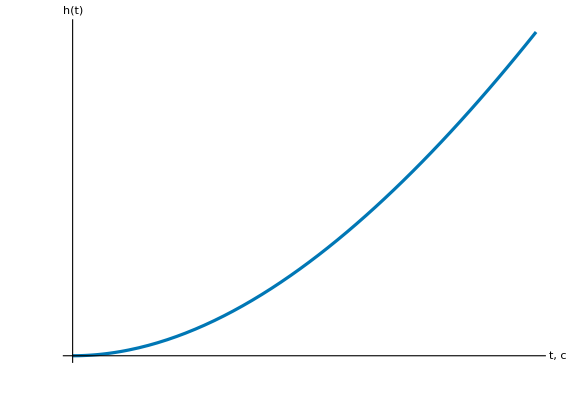

```mathematica
tickXStep =0.001;
tickYStep =0.002;
stepRespPic=Plot[{TFstep},{t, 0, maxt},
AxesStyle->Directive[Thickness[0.002],Black],
AxesLabel->{sizeText["t, с"], sizeText["h(t)"]},
GridLines->None,
AspectRatio->11/16,
PlotStyle->{{RGBColor["#0077b5"],Thickness[0.004]},{Black,dashingStyle}},
PlotRange->{{0,maxt},{0,0.02}},
PlotRangeClipping->False,
ImageSize->Large,
Ticks->{
(#&@Array[{tickXStep#,,{0.006,0.006}}&,100]),
(#&@Array[{tickYStep #,,{0.006,0.006}}&,100])
}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"step.svg";
Export[fName,stepRespPic];
```

## Bode plot

### Log Plot

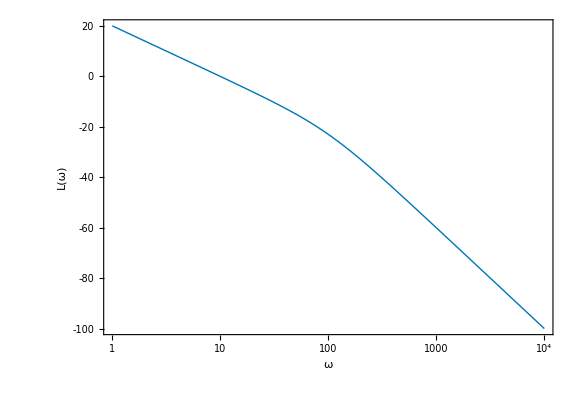

```mathematica
bodePlot=BodePlot[TF,{1,10^4},PlotRange->{{-100,20},Automatic},
PlotStyle->Thickness[0.004],
ImageSize->Large,
PlotLayout->"List"
];
ampBodePlot=RestylePlot[
bodePlot[[1]],
{RGBColor["#0077b5"],Thickness[0.004]},
AxesLabel->{sizeText["ω"],sizeText["L(ω)"]},
AxesStyle->Directive[Thickness[0.002],Black],
AspectRatio->11/16,
LabelStyle->{
FontFamily->"Arial",14,Black
},
PlotRangeClipping->False,
ImageSize->Large,
ImagePadding->{{All, All},{50, 30}}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"log-apm-freq.svg";
Export[fName,ampBodePlot]
```

D:\Development\Other Projects\elementary-dynamic-elements-of-control-systems\src\..\plots\integr-with-delay\log-apm-freq.svg

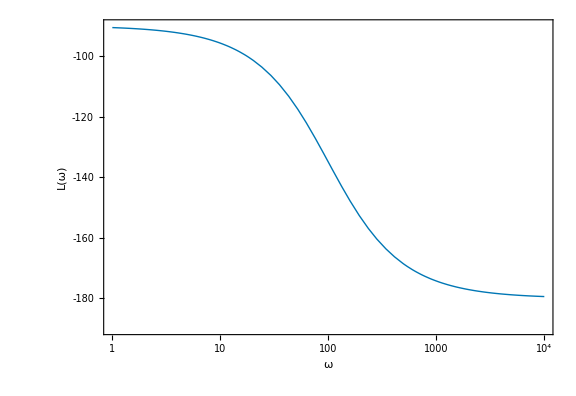

```mathematica
phaseBodePlot=RestylePlot[
bodePlot[[2]],
{RGBColor["#0077b5"],Thickness[0.004]},
PlotRange->{Automatic,{-190,0-90}},
AxesStyle->Directive[Thickness[0.002],Black],
AspectRatio->11/16,
AxesLabel->{sizeText["ω"],sizeText["L(ω)"]},
LabelStyle->{
FontFamily->"Arial",14,Black
},
PlotRangeClipping->False,
ImageSize->Large,
ImagePadding->{{All, All},{50, 30}}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"log-phase-freq.svg";
Export[fName,phaseBodePlot]
```

D:\Development\Other Projects\elementary-dynamic-elements-of-control-systems\src\..\plots\integr-with-delay\log-phase-freq.svg

### Plot

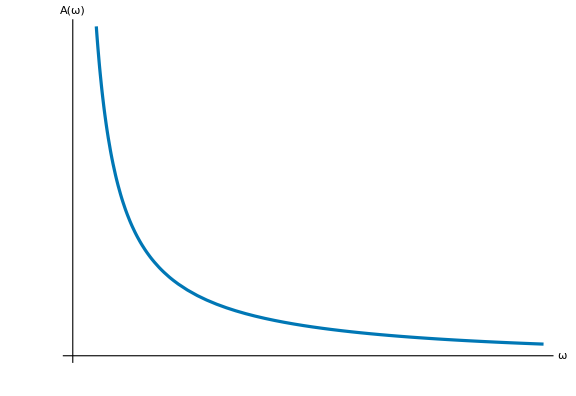

```mathematica
ampPlot=Plot[Abs[TF[I f]], {f,0, 100},
PlotRange->{{0, 100},{0,2}},
PlotStyle->{RGBColor["#0077b5"],Thickness[0.004]},
AxesLabel->{sizeText["ω"],sizeText["A(ω)"]},
LabelStyle->{
FontFamily->"Arial",14,Black
},
AxesStyle->Directive[Thickness[0.002],Black],
AspectRatio->11/16,
PlotRangeClipping->False,
ImageSize->Large,
ImagePadding->{{All, All},{50, 30}},
Ticks->{
(#&@Array[{10#,,{0.006,0.006}}&,100]),
(#&@Array[{0.1#,,{0.006,0.006}}&,100])
}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"amp-freq.svg";
Export[fName,ampPlot]
```

D:\Development\Other Projects\elementary-dynamic-elements-of-control-systems\src\..\plots\integr-with-delay\amp-freq.svg

NyquistPlot::scinf: The semicircles at infinity could not be plotted for TransferFunctionModel[{{{1000.}},s (100.+1. s)},s]. Try changing the PlotPoints or PlotRange value.

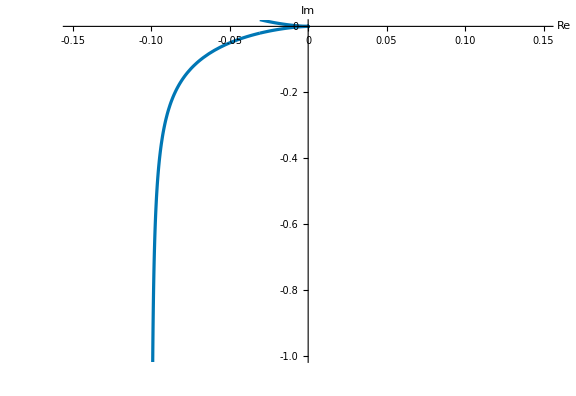

```mathematica
nyquistPlot=NyquistPlot[TF,
PlotRange->{{-0.15,.15},{-1,0}},
PlotStyle->{RGBColor["#0077b5"],Thickness[0.004]},
AxesLabel->{sizeText["Re"],sizeText["Im"]},
AxesOrigin->{0,0},
AxesStyle->Directive[Thickness[0.002],Black],
AspectRatio->11/16,
LabelStyle->{
FontFamily->"Arial",14,Black
},
PlotRangeClipping->False,
ImageSize->Large,
ImagePadding->{{All, All},{50, 30}}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"nyquist.svg";
Export[fName,nyquistPlot]
```

D:\Development\Other Projects\elementary-dynamic-elements-of-control-systems\src\..\plots\integr-with-delay\nyquist.svg